```mathematica
dbticks=Table[{l*10-5,ToString[l*10-5],{0,.005}},{l,1,4}]
fticks2=Table[{l*1000,ToString[l],{0,.005}},{l,1,7}]
```

{{5,5,{0,0.005}},{15,15,{0,0.005}},{25,25,{0,0.005}},{35,35,{0,0.005}}}

{{1000,1,{0,0.005}},{2000,2,{0,0.005}},{3000,3,{0,0.005}},{4000,4,{0,0.005}},{5000,5,{0,0.005}},{6000,6,{0,0.005}},{7000,7,{0,0.005}}}

```mathematica
Plot[{20*Log[10,Abs[SL/S0]]/.θ->90,5*Arg[SL/S0]/(k*L)/.θ->90},{f,100,3500},PlotRange->All,AxesOrigin->{f0,3}]
```

```mathematica
Tokaydiff=20*Log10[Abs[SL/S0]]/.θ->90;
```

```mathematica
Hemidactylusdiff=20*Log10[Abs[SL/S0]]/.θ->90;
```

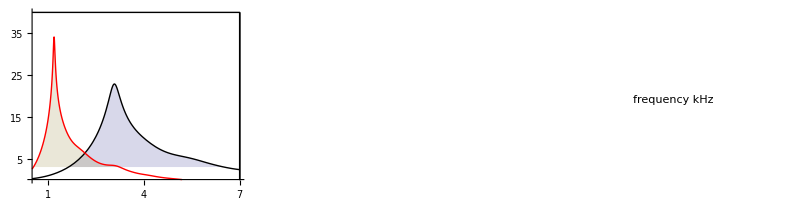

```mathematica
GraphicsRow[{Plot[{If[1643.682≤f≤6505.03,3],Hemidactylusdiff,If[542.35≤f≤3238.11,3],Tokaydiff},{f,500,7000},PlotRange->{{500,7000.01},{0,40}},PlotStyle->{None,Black,None,Red},Ticks->{fticks2,dbticks,None,None},AxesOrigin->{500,0},Filling->{2->{1},4->{3}},Epilog->{Line[{{500,40},{7000,40},{7000,0},{7000,40}}]}],Graphics[Legend[{{Graphics[{Black,Line[{{0,0},{1,0}}]}],Style["Hemidactylus",16]},{Graphics[{Red,Line[{{0,0},{1,0}}]}],Style["Tokay",16]}}]],Graphics[{Text[Style[frequency (kHz),Medium]]}]}]
```

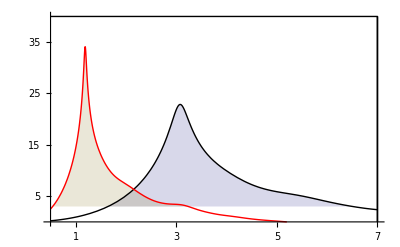

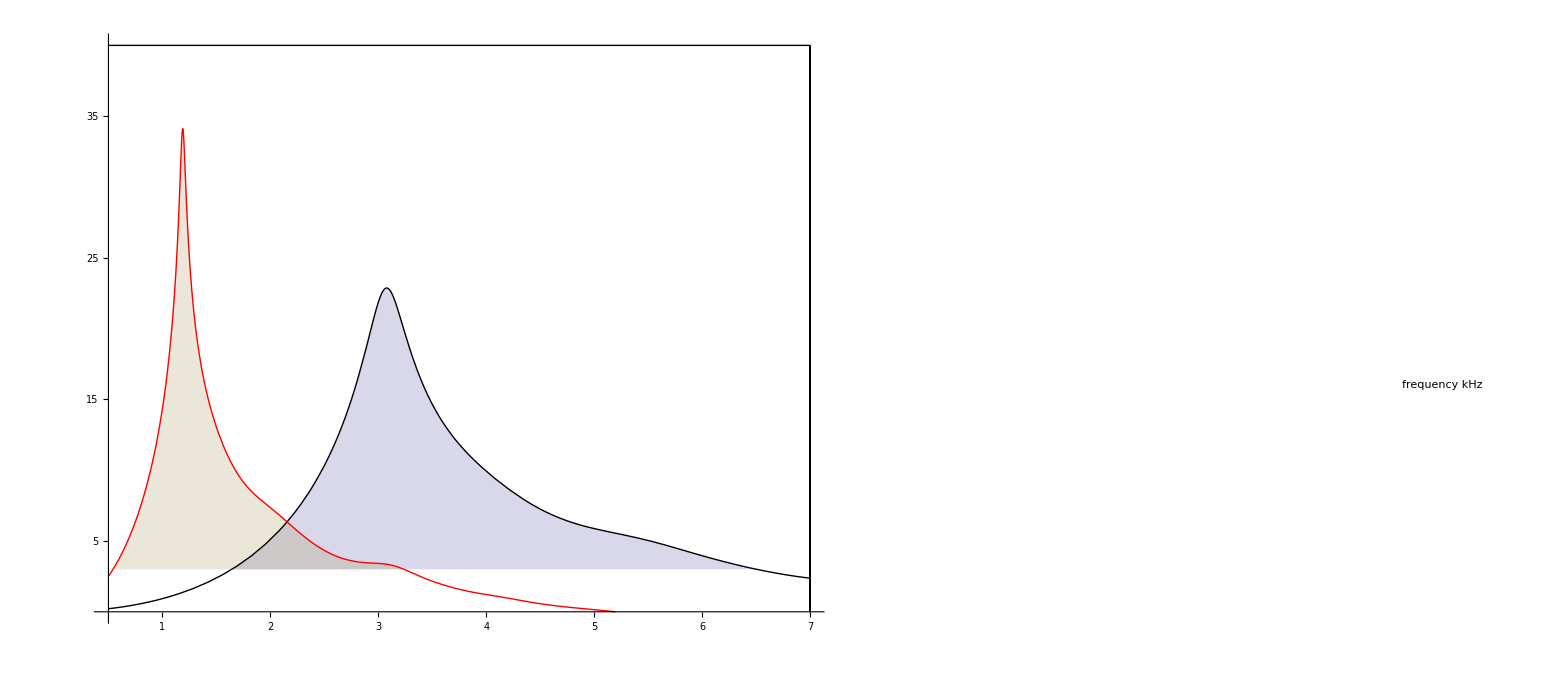

```mathematica
Graphics[{Black,Line[{{0,0},{1,0}}]}]
```

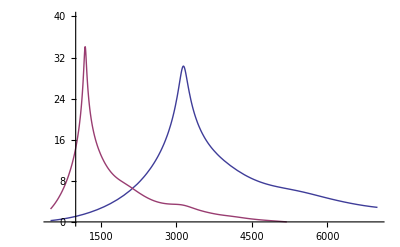

```mathematica
Plot[{Hemidactylusdiff,Tokaydiff},{f,500,7000},PlotRange->{{500,7000.01},{0,40}}]
```

{{0,0,{0,0.005}},{25,25,{0,0.005}},{50,50,{0,0.005}},{75,75,{0,0.005}},{100,100,{0,0.005}},{125,125,{0,0.005}},{150,150,{0,0.005}},{175,175,{0,0.005}},{200,200,{0,0.005}},{225,225,{0,0.005}}}

{{1000,1.,{0,0.005}},{2000,2.,{0,0.005}},{3000,3.,{0,0.005}},{4000,4.,{0,0.005}},{5000,5.,{0,0.005}},{6000,6.,{0,0.005}},{7000,7.,{0,0.005}}}

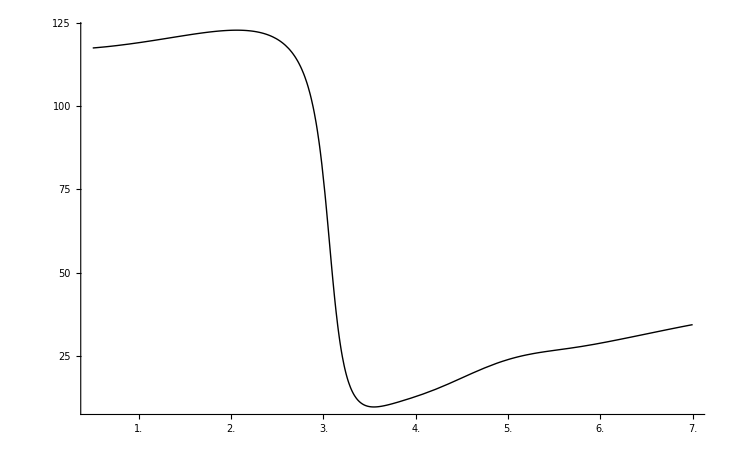

```mathematica
tticks=Table[{l*25-25,ToString[l*25-25],{0,.005}},{l,1,10}]
fticks=Table[{l*1000,ToString[N[l]],{0,.005}},{l,1,7}]
Plot[{10^6*Arg[SL/S0]/ω/.θ->90},{f,500,7000},PlotRange->All,AxesOrigin->{500,0},Ticks->{fticks,tticks},PlotRange->All,PlotStyle->Black]
```

{{500,0.5,{0,0.005}},{1000,1.,{0,0.005}},{1500,1.5,{0,0.005}},{2000,2.,{0,0.005}},{2500,2.5,{0,0.005}},{3000,3.,{0,0.005}},{3500,3.5,{0,0.005}},{4000,4.,{0,0.005}}}

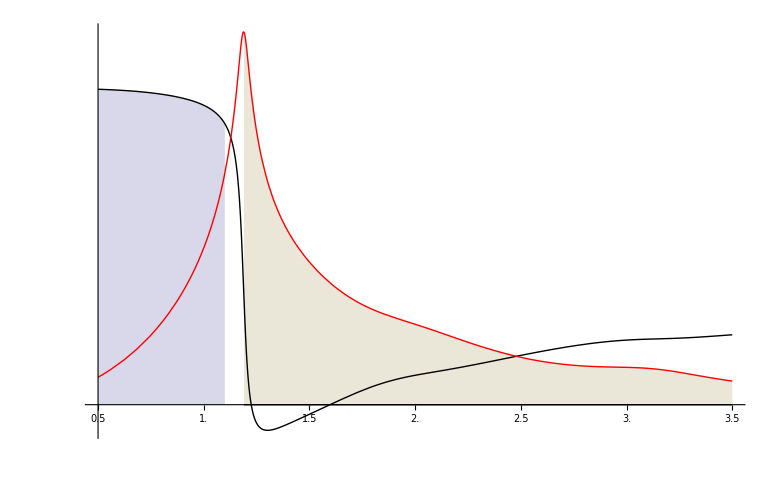

```mathematica
fticks=Table[{l*500,ToString[N[l/2]],{0,.005}},{l,1,8}]
Plot[{8*Arg[SL/S0]/Arg[pL/p0]/.θ->90,If[500≤f≤1100,0],20*Log10[Abs[SL/S0]]/.θ->90,
If[1190≤f≤7000,0]},{f,500,3500},PlotRange->All,AxesOrigin->{500,0},PlotStyle->{Black,None,Red},Filling->{1->{2},3->{4}},Ticks->{fticks,None}]
```

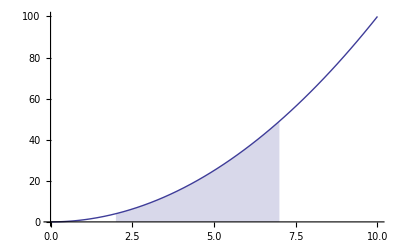

```mathematica
Plot[{x^2,If[2≤x≤7,0]},{x,0,10},PlotStyle->{Automatic,None},Filling->{1->{2}}]
```

```mathematica
tticks=Table[{l*50-200,ToString[l*50-200],{0,.005}},{l,1,7}]
dticks=Table[{(l-1)*90-180,ToString[(l-1)*90-180],{0,.01}},{l,1,5}]
```

{{-150,-150,{0,0.005}},{-100,-100,{0,0.005}},{-50,-50,{0,0.005}},{0,0,{0,0.005}},{50,50,{0,0.005}},{100,100,{0,0.005}},{150,150,{0,0.005}}}

{{-180,-180,{0,0.01}},{-90,-90,{0,0.01}},{0,0,{0,0.01}},{90,90,{0,0.01}},{180,180,{0,0.01}}}

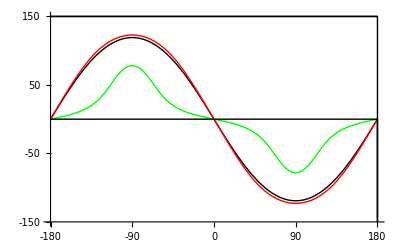

```mathematica
prange=150;
Plot[{10^6*Arg[S0/SL]/ω/.f->1000,10^6*Arg[S0/SL]/ω/.f->2000,10^6*Arg[S0/SL]/ω/.f->3000},{θ,-180,180},PlotRange->prange,PlotStyle->{Black,Red,Green},AxesOrigin->{-180,-prange},Ticks->{dticks,tticks},Epilog->{Line[{{-180,0},{180,0},{180,-prange},{180,prange},{-180,prange},{180,prange}}]},PlotLegend->{Style["1kHz",Black,18],Style["2kHz",Black,18],Style["3kHz",Black,18]},LegendPosition->{-2.0,-.25}]
```

```mathematica
10^6*Arg[S0/SL]/ω/.{f->2000,θ->-90}
```

122.855